This script is a part of ANGEL project.
V 1.0
2018.05.10
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];(* Clearing all variables *)
Needs["JLink`"];(* Not to be any problems with exporting *)
ReinstallJava[JVMArguments -> "-Xmx512m"];(* DO NOT TOUCH! *)
```

```mathematica
Kprt=-136; (* K^prt for current resonance *)
```

```mathematica
importDir = "";(* Directory for importing data *)
exportDir = "";(* Directory for exporting data *)
```

```mathematica
phaseColumnName="Theta"; (* Name of column in data file with phase *)
frequencyColumnName="Fext";(* Name of column in data file with frequency *)
timeRoundColumnName="TimeAll";(* Name of column in data file with time *)
timeKineticsColumnName="Time";(* Name of column in data file with time *)
PrescanDataFileName="Prescan.dat";(* Name of file with prescan *)
RoundDataFileName="Kinetic_Round_1.dat";(* Name of file with first round *)
KineticsDataFileName="Kinetic.dat";(* Name of file with slow kinetics *)
```

```mathematica
lorenz[y0_,A_,μ_, σ_, x_]:=y0 + (2A)/π×σ/(4 (x-μ)^2+σ^2);(* Lorenz function *)
lorenzInverse[y0_,A_,μ_, σ_, y_,sgn_]:=Sign[sgn]×√((2 A σ)/(4 π (y-y0))-σ^2/4)+μ;(* Inverse Lorenz function *)
paraboloid[y0_,A_,μ_,x_] := y0 + A(x-μ)^2;(* Paraboloid *)
```

```mathematica
PreScanDataNames=Import[FileNameJoin[{NotebookDirectory[ ],importDir,PrescanDataFileName}]][[1]];(* Importing prescan file header *)
PreScanData=Import[FileNameJoin[{NotebookDirectory[ ],importDir,PrescanDataFileName}]][[2;;]];(* Importing prescan file data *)
```

```mathematica
PreScanFrequency=PreScanData[[All,Position[PreScanDataNames,frequencyColumnName][[1,1]]]];(* Getting frequency column *)
PreScanTheta=PreScanData[[All,Position[PreScanDataNames,phaseColumnName][[1,1]]]];(* Getting phase column *)
PreScanData=Transpose[{PreScanFrequency,PreScanTheta}];(* Forming prescan data *)
```

```mathematica
PreScanLorenzFit=NonlinearModelFit[(* Fitting prescan data with lorenz *)
PreScanData,lorenz[y0,A,μ, σ,x],
{{y0,Max[PreScanTheta]},
{A,Min[PreScanTheta]-Max[PreScanTheta]},
{μ,PreScanFrequency[[Position[PreScanTheta,Min[PreScanTheta]][[1,1]]]]},
{σ,10}},
x];
parametersTablePreScanLorenzFit=PreScanLorenzFit["ParameterTable"];(* Getting fited parameters and their errors *)
y0LorenzFit=parametersTablePreScanLorenzFit[[1,1,2,2]];δy0LorenzFit=parametersTablePreScanLorenzFit[[1,1,2,3]];
ALorenzFit=parametersTablePreScanLorenzFit[[1,1,3,2]];δALorenzFit=parametersTablePreScanLorenzFit[[1,1,3,3]];
μLorenzFit=parametersTablePreScanLorenzFit[[1,1,4,2]];δμLorenzFit=parametersTablePreScanLorenzFit[[1,1,4,3]];
σLorenzFit=parametersTablePreScanLorenzFit[[1,1,5,2]];δσLorenzFit=parametersTablePreScanLorenzFit[[1,1,5,3]];
PreScanFitPlot=Show[(* Plotting round data and fittings *)
ListPlot[PreScanData,PlotLabel->"Phase fitting: Lorenz(Red)",AxesLabel->{"Frequency[Hz]","Phase[Deg]"},PlotRange->All],
Plot[lorenz[y0LorenzFit,ALorenzFit,μLorenzFit, σLorenzFit,x],{x,Min[PreScanFrequency],Max[PreScanFrequency]},ColorFunction->Function[{x,y},Red],PlotRange->All]
];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"PreScan_DataFit.png"}],PreScanFitPlot];(* Exporting plot from above *)
```

```mathematica
FastKineticDataNames=Import[FileNameJoin[{NotebookDirectory[ ],importDir,RoundDataFileName}]][[1]];(* Importing fast kinetics file header *)
FastKineticsData=Import[FileNameJoin[{NotebookDirectory[ ],importDir,RoundDataFileName}]][[2;;]];(* Importing fast kinetics data *)
FastKineticsTime=FastKineticsData[[All,Position[FastKineticDataNames,timeRoundColumnName][[1,1]]]];(* Getting time column *)
FastKineticsTheta=FastKineticsData[[All,Position[FastKineticDataNames,phaseColumnName][[1,1]]]];(* Getting phase column *)
FastKineticsData=Transpose[{FastKineticsTime,FastKineticsTheta}];(* Forming fast kinetics data *)
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"FastKineticsData" <>ToString[1]<>"_Raw.png"}],
ListPlot[FastKineticsData,PlotLabel->"FastKinetics Data" <>ToString[1],AxesLabel->{"Time[s]","Phase[deg]"},ImageSize->Medium,PlotRange->All]];(* Just to be shure everything goes well *)
```

```mathematica
TimeMinTheta=FastKineticsTime[[Position[FastKineticsTheta,Min[FastKineticsTheta]][[1,1]]]];(* Finding phase minimum *)
(* Changing parameters for better fitting *)
ALorenzFitFix=1/2 π (Min[FastKineticsTheta]-y0LorenzFit) σLorenzFit;
y0LorenzFitFix=Min[FastKineticsTheta]-(2 ALorenzFit)/(π σLorenzFit);
parametersString="Lorenz fitting ( y0 + 2A/Pi * σ/(4 (x-μ)^2+σ^2) ):"<>"\n\t"<>(* Forming a string with fited parameters and their errors *)
"y0 = "<>ToString[y0LorenzFit]<>" ± "<>ToString[δy0LorenzFit]<>", t.m. "<>ToString[100×Abs[δy0LorenzFit/y0LorenzFit]]<>" %"<>"\n\t"<>
"A = "<>ToString[ALorenzFit]<>" ± "<>ToString[δALorenzFit]<>", t.m. "<>ToString[100×Abs[δALorenzFit/ALorenzFit]]<>" %"<>"\n\t"<>
"μ/10^3 = "<>ToString[μLorenzFit/10^3]<>" ± "<>ToString[δμLorenzFit]<>", t.m. "<>ToString[100×Abs[δμLorenzFit/μLorenzFit]×10^3]<>"×10^(-3) %"<>"\n\t"<>
"σ = "<>ToString[σLorenzFit]<>" ± "<>ToString[δσLorenzFit]<>", t.m. "<>ToString[100×Abs[δσLorenzFit/σLorenzFit]]<>" %"<>"\n"<>
"y0Fix = "<>ToString[y0LorenzFitFix]<>"\n"<>"AFix = "<>ToString[ALorenzFitFix]<>"\n";
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"FastKineticsData"<>ToString[1]<>"_Fit.txt"}],parametersString];(* Exporting string from above *)
(* Forming data for kinetics fit *)
TemperatureLorenzFromTimeRaw=Table[{FastKineticsTime[[i]],lorenzInverse[y0LorenzFit,ALorenzFit,μLorenzFit, σLorenzFit,FastKineticsTheta[[i]],-FastKineticsTime[[i]]+TimeMinTheta]},
{i,1,Length[FastKineticsTime]}];
TemperatureLorenzFromTimeAFix=Table[{FastKineticsTime[[i]],lorenzInverse[y0LorenzFit,ALorenzFitFix,μLorenzFit, σLorenzFit,FastKineticsTheta[[i]],-FastKineticsTime[[i]]+TimeMinTheta]},
{i,1,Length[FastKineticsTime]}];
TemperatureLorenzFromTimeY0Fix=Table[{FastKineticsTime[[i]],lorenzInverse[y0LorenzFitFix,ALorenzFit,μLorenzFit, σLorenzFit,FastKineticsTheta[[i]],-FastKineticsTime[[i]]+TimeMinTheta]},
{i,1,Length[FastKineticsTime]}];
(* Frequency -> ΔTemperature *)
TemperatureLorenzFromTimeRaw[[All,2]]=1/Kprt(TemperatureLorenzFromTimeRaw[[All,2]]-TemperatureLorenzFromTimeRaw[[1,2]]);
TemperatureLorenzFromTimeAFix[[All,2]]=1/Kprt(TemperatureLorenzFromTimeAFix[[All,2]]-TemperatureLorenzFromTimeAFix[[1,2]]);
TemperatureLorenzFromTimeY0Fix[[All,2]]=1/Kprt(TemperatureLorenzFromTimeY0Fix[[All,2]]-TemperatureLorenzFromTimeY0Fix[[1,2]]);
```

```mathematica
TemperatureLorenzKineticsExport=Prepend[Transpose[Join[Transpose[TemperatureLorenzFromTimeRaw],Transpose[TemperatureLorenzFromTimeAFix],Transpose[TemperatureLorenzFromTimeY0Fix]]],{"Time[s] Lorenz "<>ToString[1]<>", Raw","ΔTemperature[C], Raw","Time[s] Lorenz "<>ToString[1]<>", Afix","ΔTemperature[C], Afix","Time[s] Lorenz "<>ToString[1]<>", Y0fix","ΔTemperature[C], y0Fix"}];
(* Exporting calculated data *)
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"FastKineticsKinetics"<>".xlsx"}],TemperatureLorenzKineticsExport];
(* Plotting round kinetics data *)
TemperatureLorenzKineticsPlotRound= ListPlot[Evaluate[{TemperatureLorenzFromTimeRaw,TemperatureLorenzFromTimeAFix,TemperatureLorenzFromTimeY0Fix}],
PlotLabel->"Lorenz Raw(Blue), AFix(Orange), \nY0Fix(Green) phase fitting for round "<>ToString[1],AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"FastKineticsKineticsRound_"<>ToString[1]<>".png"}],TemperatureLorenzKineticsPlotRound];(* Exporting plot from above *)
```

```mathematica
(* Getting plots for kinetics and exporting them *)
TemperatureLorenzKineticsPlotAllRaw= ListPlot[TemperatureLorenzFromTimeRaw,PlotLabel->"Lorenz phase fitting Raw",AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All];
TemperatureLorenzKineticsPlotAllAFix= ListPlot[TemperatureLorenzFromTimeAFix,PlotLabel->"Lorenz phase fitting AFix",AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All];
TemperatureLorenzKineticsPlotAllY0Fix= ListPlot[TemperatureLorenzFromTimeY0Fix,PlotLabel->"Lorenz phase fitting Y0Fix",AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"FastKineticsKineticsRaw"<>".png"}],TemperatureLorenzKineticsPlotAllRaw];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"FastKineticsKineticsAFix"<>".png"}],TemperatureLorenzKineticsPlotAllAFix];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"FastKineticsKineticsY0Fix"<>".png"}],TemperatureLorenzKineticsPlotAllY0Fix];
```

```mathematica
SlowKineticDataNames=Import[FileNameJoin[{NotebookDirectory[ ],importDir,KineticsDataFileName}]][[1]];(* Importing slow kinetics file header *)
SlowKineticsData=Import[FileNameJoin[{NotebookDirectory[ ],importDir,KineticsDataFileName}]][[2;;]];(* Importing slow kinetics data *)
SlowKineticsTime=SlowKineticsData[[All,Position[SlowKineticDataNames,timeKineticsColumnName][[1,1]]]];(* Getting time column *)
SlowKineticsFrequency=SlowKineticsData[[All,Position[SlowKineticDataNames,frequencyColumnName][[1,1]]]];(* Getting frequency column *)
SlowKineticsData=Transpose[{SlowKineticsTime,SlowKineticsFrequency}];(* Forming slow kinetics data *)
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"SlowKineticsData" <>"_Raw.png"}],
ListPlot[SlowKineticsData,PlotLabel->"SlowKinetics Data",AxesLabel->{"Time[s]","Frequency[Hz]"},ImageSize->Medium,PlotRange->All]];(* Just to be shure everything goes well *)
```

```mathematica
StaringFrequency=PreScanFrequency[[Position[PreScanTheta,Min[PreScanTheta]][[1,1]]]];(* Frequency before kinetics *)
TemperatureKineticsFromTime=SlowKineticsData;(* Preparing data *)
TemperatureKineticsFromTime[[All,2]]=1/Kprt(TemperatureKineticsFromTime[[All,2]]-StaringFrequency);(* Evaluating data *)
```

```mathematica
TemperatureKineticsExport=Prepend[Transpose[Join[Transpose[TemperatureKineticsFromTime]]],{"Time[s] Kinetics","ΔTemperature[C]"}];(* Preparing data for export *)
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"TemperatureKinetics"<>".xlsx"}],TemperatureKineticsExport];(* Exporting calculated data *)
```

```mathematica
plt=ListPlot[{TemperatureLorenzFromTimeRaw,TemperatureLorenzFromTimeAFix,TemperatureLorenzFromTimeY0Fix,TemperatureKineticsFromTime},PlotRange->All,ImageSize->Large,PlotMarkers->{"*","*","*","*"},PlotLabel->"Red - Long"];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"Kinetics.png"}],plt];
```

```mathematica
Temperature=Import[FileNameJoin[{NotebookDirectory[ ],importDir,"Temperature.dat"}]][[2;;]];
Temperature[[All,2]]=Temperature[[All,2]]-Temperature[[1,2]];
plt=ListPlot[{Temperature,TemperatureLorenzFromTimeRaw,TemperatureKineticsFromTime},PlotRange->All,ImageSize->Large,PlotMarkers->{"*","*","😐"},PlotLabel->"Blue - Temperature, Orange - Fast, Green - Slow"];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"Temperatures.png"}],plt];
```

```mathematica
TemperatureFunc=Interpolation[Temperature,InterpolationOrder->1];
```

```mathematica
Off[Power::infy];
FastDelta=Table[{TemperatureLorenzFromTimeRaw[[i,1]],(TemperatureLorenzFromTimeRaw[[i,2]]-TemperatureFunc[TemperatureLorenzFromTimeRaw[[i,1]]])/TemperatureFunc[TemperatureLorenzFromTimeRaw[[i,1]]]×100},{i,1,Length[TemperatureLorenzFromTimeRaw]}];
SlowDelta=Table[{TemperatureKineticsFromTime[[i,1]],(TemperatureKineticsFromTime[[i,2]]-TemperatureFunc[TemperatureKineticsFromTime[[i,1]]])/TemperatureFunc[TemperatureKineticsFromTime[[i,1]]]×100},{i,1,Length[TemperatureKineticsFromTime]}];
```

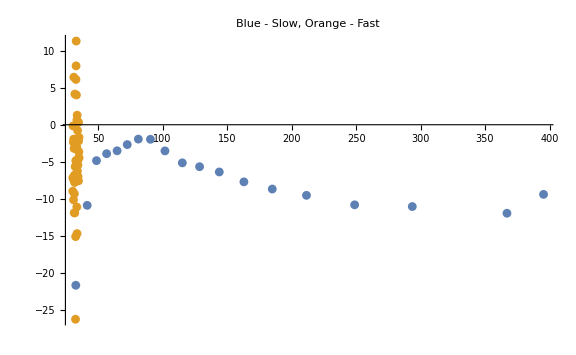

```mathematica
plt=ListPlot[{SlowDelta,FastDelta[[300;;]]},PlotRange->All,ImageSize->Large,PlotLabel->"Blue - Slow, Orange - Fast"]
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"TemperaturesDelta.png"}],plt];
```